```mathematica
μ=8/9;ℏc=197;E2=3;
```

```mathematica
κ[En_]:=Sqrt[(2μ (En-E2))/ℏc^2];
wavebound[En_,r_,l_]:=SphericalHankelH1[l,κ[En] r];
```

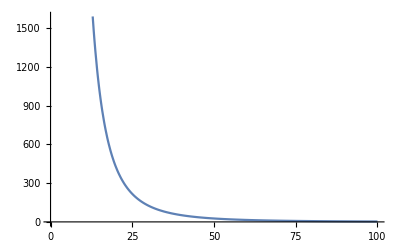

```mathematica
Plot[Re[wavebound[1,x,2]],{x,0,100}]
```

```mathematica
κ[1]
```

(4 ⅈ √2)/591

```mathematica
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
waveres[En_?NumericQ,r_,l_]:=SphericalHankelH1[l,k[En] r];
```

```mathematica
ks[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
wavescat[En_,r_,δ_,l_]:=(Cos[δ]SphericalBesselJ[l,ks[En] r]-Sin[δ] SphericalBesselY[l,ks[En] r]);
```